```mathematica
NewtonRapson[Po_,Tol_,n_,F_]:=
	Module[{i=1,Y,t=Po},
		While[i≤n,
			Y=(t-(F[t]/F'[t]));

				Print["En la iteracion ",i ," el valor de X es ",N[Y,15]];
Print["f' es  =",N[F'[t],20]," y= ",N[F[t],20]," con t=",N[t,20]];
				If[Abs[Y-t]<Tol,N[Return[Y],30]];
				Print["Numero maximo de iteraciones excedido"];
			i++;
			t=Y;

		];
Print[N[Y,30]];
	];
```

```mathematica
F[x_]:=Log[x-1]+Cos[x-1];
```

```mathematica
N[NewtonRapson[1.65,0.0001,20,F],20]
```

En la iteracion 1 el valor de X es 1.25858

f' es  =0.933275 y= 0.365301 con t=1.65

Numero maximo de iteraciones excedido

En la iteracion 2 el valor de X es 1.3654

f' es  =3.61154 y= -0.38579 con t=1.25858

Numero maximo de iteraciones excedido

En la iteracion 3 el valor de X es 1.39599

f' es  =2.37938 y= -0.0727741 con t=1.3654

Numero maximo de iteraciones excedido

En la iteracion 4 el valor de X es 1.39774

f' es  =2.13961 y= -0.00375424 con t=1.39599

Numero maximo de iteraciones excedido

En la iteracion 5 el valor de X es 1.39775

f' es  =2.12685 y= -0.0000112081 con t=1.39774

1.39775

```mathematica
]
```

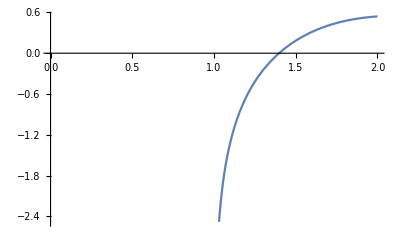

```mathematica
Plot[Log[x-1]+Cos[x-1],{x,0,2}]
```

```mathematica
D[Log[x-1]+Cos[x-1],x]
```

1/(-1+x)+Sin[1-x]

```mathematica
1/(-1+1.3654)+Sin[1-1.3654]
```

2.3794

```mathematica
Log[1.3654-1]+Cos[1.3654-1]
```

-0.0727817